# Ejercicios 1

## Programa

```mathematica
(*programa para máximos y mínimos*)
maxminint[f_,a_,b_]:=Module[{},
d1=D[f,x];
sol=NSolve[D[f,x]==0 && a<x<b,x];
d2=D[f,{x,2}];
d2/.sol;
seg=d2/.sol;

Table[If[seg[[i]]>0,Print["Minimo en x = ",x/.sol[[i]]],
Print["Maximo en =  ",x/.sol[[i]]]],{i,Length[sol]}];
Print[Plot[f,{x,Min[x/.sol]-2,Max[x/.sol]+2}]]
]
```

## 13

```mathematica
(*programa para máximos y mínimos*)
(*ejericio #13*)
maxminint[f_,a_,b_]:=Module[{},
d1=D[f,x];
sol=NSolve[D[f,x]==0 && a<x<b,x];
d2=D[f,{x,2}];
d2/.sol;
seg=d2/.sol;

Table[If[seg[[i]]>0,Print["Minimo en x = ",x/.sol[[i]]],
Print["Maximo en =  ",x/.sol[[i]]]],{i,Length[sol]}];
Print[Plot[f,{x,Min[x/.sol]-2,Max[x/.sol]+2}]]
```

```mathematica
f=(2 x^2)/(x-2);
```

Maximo en =  0.

Minimo en x = 4.

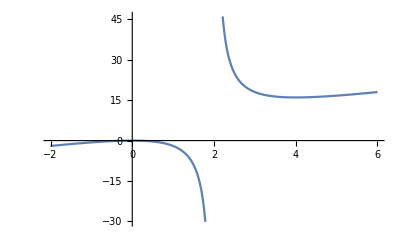

```mathematica
maxminint[f,-∞,∞]
```

## 14

```mathematica
(*programa para máximos y mínimos*)
(*ejericio #14*)
maxminint[f_,a_,b_]:=Module[{},
d1=D[f,x];
sol=NSolve[D[f,x]==0 && a<x<b,x];
d2=D[f,{x,2}];
d2/.sol;
seg=d2/.sol;

Table[If[seg[[i]]>0,Print["Minimo en x = ",x/.sol[[i]]],
Print["Maximo en =  ",x/.sol[[i]]]],{i,Length[sol]}];
Print[Plot[f,{x,Min[x/.sol]-2,Max[x/.sol]+2}]]
]
```

```mathematica
f= 1-x-(x^2-1);
```

Maximo en =  -0.5

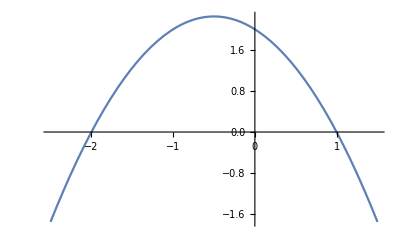

```mathematica
maxminint[f,-∞,∞]
```

```mathematica
f/.sol (*distancia máxima entre las 2 distancias*)
```

{2.25}

## 15

```mathematica
(*programa para máximos y mínimos*)
(*ejericio #15*)
maxminint[f_,a_,b_]:=Module[{},
d1=D[f,x];
sol=NSolve[D[f,x]==0 && a<x<b,x];
d2=D[f,{x,2}];
d2/.sol;
seg=d2/.sol;

Table[If[seg[[i]]>0,Print["Minimo en x = ",x/.sol[[i]]],
Print["Maximo en =  ",x/.sol[[i]]]],{i,Length[sol]}];
Print[Plot[f,{x,Min[x/.sol]-2,Max[x/.sol]+2}]]
]
```

```mathematica
f= 100(1+Cos[x])Sin[x];
```

Maximo en =  1.0472

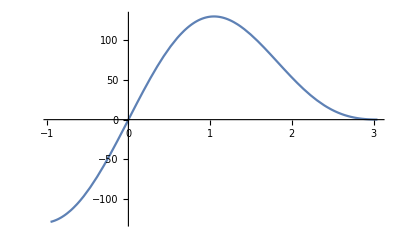

```mathematica
maxminint[f,0, π/2]
```

```mathematica
(x/.sol)  180/π
```

{60.}

## Longitud de arco

```mathematica
(*programa para realizar longitud de arco con una integral definida*)
(**)
longarc[f_,a_,b_]:=Module[{},
N[∫_a^b √(1+(D[f,x])^2)ⅆx]

]
```

```mathematica
f=x^2;
```

```mathematica
longarc[f,-1,3]
```

11.226

```mathematica
(*programa para realizar longitud de arco con una integral definida*)
(*con listas*)
longarc[f_,a_]:=Module[{},
N[∫_a[[1]]^a[[2]] √(1+(D[f,x])^2)ⅆx]

]
```

```mathematica
f=x^2;
```

```mathematica
longarc[f,{-1,3}]
```

11.226

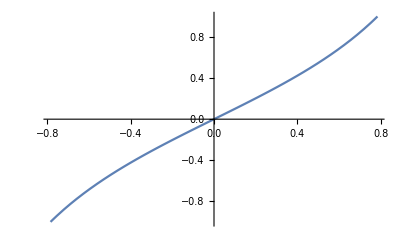

```mathematica
Plot[Tan[x],{x,-π/4,π/4}]
```

#### ejercicio 13 longitud de arco

```mathematica
(*programa para realizar longitud de arco con una integral definida*)
(*ejercicio 13*)
longarc[f_,a_,b_]:=Module[{},
N[∫_a^b √(1+(D[f,x])^2)ⅆx]

]
```

## Calculo de Áreas

#### Ejercicios 31-48

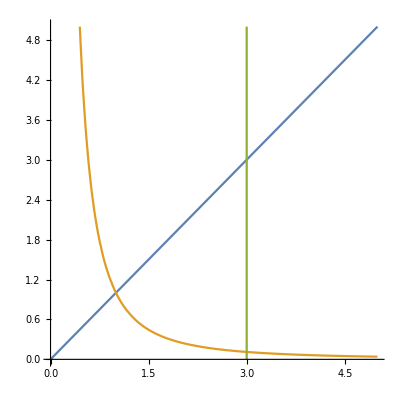

```mathematica
ContourPlot[{y==x,y==1/x^2,x==3},{x,0,5},{y,0,5},Frame->False,Axes->True]
```

```mathematica
NSolve[{y==x,y==1/x^2},{x,y},Reals](*Sistema de ecuaciones intersección de la ecuacion*)
```

{{x→1.,y→1.}}

```mathematica
NSolve[{y==1/x^2,x==3},{x,y},Reals]
```

{{x→3.,y→0.111111}}

```mathematica
NSolve[{y== x,x==3},{x,y},Reals]
```

{{x→3.,y→3.}}

```mathematica
N[∫_1^3 ∫_(1/x^2)^x 1ⅆyⅆx]
```

3.33333

#### ejercicio 32

```mathematica
N[∫_1^9 ∫_(1/x^2)^(x^2) 9ⅆyⅆx]
```

2176.

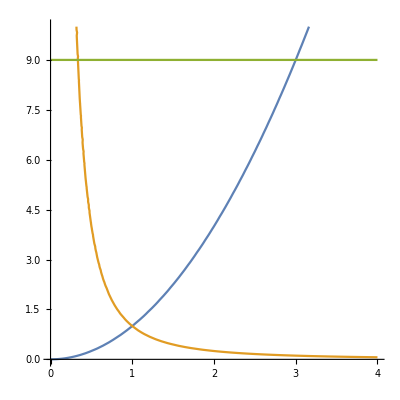

```mathematica
ContourPlot[{y==x^2,y==1/x^2,y==9},{x,0,4},{y,0,10},Frame->False,Axes->True]
```

```mathematica
NSolve[{y==x^2,y==1/x^2&& x≥0 },{x,y},Reals](*Sistema de ecuaciones intersección de la ecuacion*)
```

{{x→1.,y→1.}}

```mathematica
N[∫_1^9 ∫_(1/(√y))^(√y) 1ⅆxⅆy]
```

13.3333

#### ejercicio 43

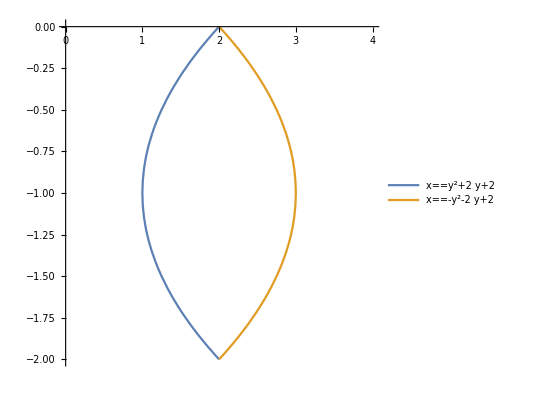

```mathematica
ContourPlot[{x==y^2+2y+2,x== -y^2-2y+2},{x,0,4},{y,-2,0},Frame->False,Axes->True,PlotLegends->"Expressions"]
(*con Plot legends mostramos que limite es el superior y el inferior línea amarilla es el límite superior de la primer integraldebido a que esta más adelante de la gráfica*)
```

```mathematica
NSolve[{x==y^2+2y+2,x== -y^2-2y+2},{x,y},Reals]
```

{{x→2.,y→-2.},{x→2.,y→0.}}

```mathematica
N[∫_-2^0 ∫_(y^2+2y+2)^(-y^2-2y+2) 1ⅆxⅆy,10]
```

2.666666667

#### ejercicio 44

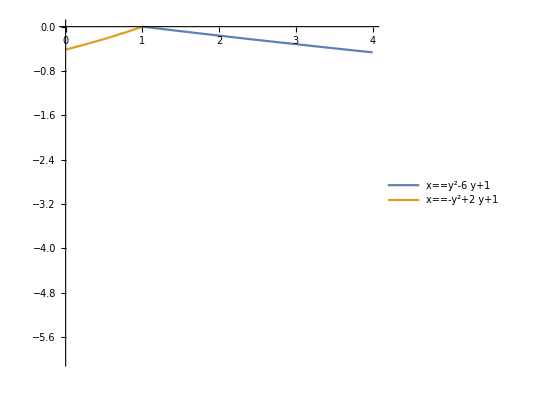

```mathematica
ContourPlot[{x==y^2-6y+1, x==-y^2+2y+1},{x,0,4},{y,-6,0},Frame->False,Axes->True,PlotLegends->"Expressions"]
(*con Plot legends mostramos que limite es el superior y el inferior línea amarilla es el límite superior de la primer integraldebido a que esta más adelante de la gráfica*)
```

```mathematica
NSolve[{x==y^2-6y+1,x== -y^2+2y+1},{x,y},Reals]
```

{{x→-7.,y→4.},{x→1.,y→0.}}

```mathematica
N[∫_-6^0 ∫_(y^2-6 y+1)^(-y^2-6 y+1) 1ⅆxⅆy,10]
```

NIntegrate::inumr: The integrand -2 y^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-6,0}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate[-2 y^2,{y,-6,0},WorkingPrecision→20.,AccuracyGoal→∞,PrecisionGoal→10.]